#### Preamble

```mathematica
ClearAll@@{$Context<>"*"}
SetDirectory[NotebookDirectory[]]
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; 
StartScheduledTask[saveTask] (*Saves nb each 15 minutes*) ;

<<"MaTeX`"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Maxima_Minima.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optics_Mie.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/jet_jet-extended.wls"
```

/home/juanathan/Documentos/MSc_Thesis/3-FEM-Calc/3-Incrusted

#### Plots format

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
colors[[1]] = ColorData[3,2];
PrependTo[colors,Black];
```

```mathematica
fs=9;
cdata3 = Table[ColorData[3,i],{i,10}];cdata3[[3]] = Purple;
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
```

```mathematica
graphsOpts:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->colors}
graphsOptsDash:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->Table[Directive[Dashed,colors[[i]]],{i,10}]}
```

```mathematica
graphsOptsPolar:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
graphsOptsPolarDashed:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[Dashed,PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
```

```mathematica
graphsOptsDensity := { BaseStyle -> texStyle, FrameStyle -> Black, PlotRange -> Full,  ColorFunctionScaling -> True, ColorFunction -> JetExtended, Mesh -> None, ImageSize -> 150, PlotRangePadding -> None  }
graphsOptsDensityExport :={PlotLegends->None,FrameTicks->None, BaseStyle -> texStyle, FrameStyle -> Black, PlotRange -> Full,  ColorFunctionScaling -> False, ColorFunction -> JetExtended, Mesh -> None, ImageSize -> 150, PlotRangePadding -> None}
```

#### Sorting Functions

```mathematica
maxPair[list_,ind_]:= SortBy[list, #[[ind]]&][[-1,{1,ind}]]
makePairs[list_,ind_]:=Map[Table[#[[;;,{1,i}]],{i,ind}]&,list]
```

Far Field S (Normal X)

```mathematica
radius = 12.5;

cases = {7,6,5,1,2,3,4};
data = FileNames["3*csv","*s"];
data = data[[cases]];
data//TableForm

data =Drop[Import[#,"Data"],8]&/@ data;
data = Transpose@Map[Partition[#,51]&,data]; (*Separete eat wlength value*)

data//Dimensions
```

Internal-s/3-Abs-FarX-p75.csv
Internal-s/3-Abs-FarX-p50.csv
Internal-s/3-Abs-FarX-p25.csv
Internal-s/3-Abs-FarX-00.csv
Internal-s/3-Abs-FarX-m25.csv
Internal-s/3-Abs-FarX-m50.csv
Internal-s/3-Abs-FarX-m75.csv

{4,7,51,2}

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];
```

3.6418

{{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8]},{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8]},{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8]},{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8]}}

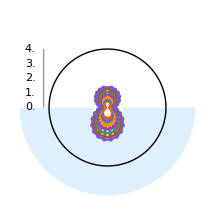
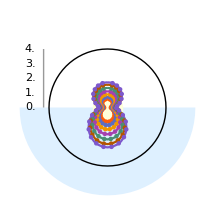
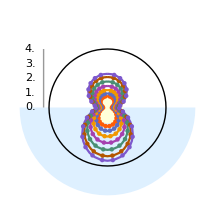
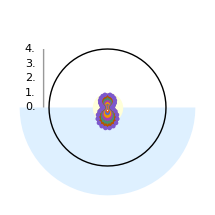

```mathematica
max = Max[#[[;;,;;,2]]]&/@data;
max = Max[max]
case = Table[i,{4},{i,.75,-.75,-.25}];
colorsPlot = {#,#,#,#}&@  colors[[2;;Length[data[[1]]]+1]]

plots = MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->max*1.65,
PolarAxesOrigin->{{Left,Up},max},
PlotStyle->Table[Directive[PointSize[.015],i],{i,#3}],
Evaluate[graphsOptsPolar],
PolarTicks->{None,Automatic},
Prolog->{LightBlue,Disk[{0,0}, max*1.65,{0,-Pi}],LightYellow,Disk[1*{0,0}/3.5,max /3.5]}
]&,
{data,case,colorsPlot}]
```

```mathematica
angle = ToString/@ {15,38,42,75}
MapIndexed[( name = angle[[First[#2]]];
  name = FileNameJoin[{"Internal-sp","5-Far-S","5-Far-SX-"<>name<>".pdf"}];
  Export[name,#1]
  )&, plots]
```

{15,38,42,75}

{Internal-sp/5-Far-S/5-Far-SX-15.pdf,Internal-sp/5-Far-S/5-Far-SX-38.pdf,Internal-sp/5-Far-S/5-Far-SX-42.pdf,Internal-sp/5-Far-S/5-Far-SX-75.pdf}

Far Field S (Normal Y)

```mathematica
radius = 12.5;

cases = {7,6,5,1,2,3,4};
data = FileNames["4*csv","*s"];
data = data[[cases]];
data//TableForm

data =Drop[Import[#,"Data"],8]&/@ data;
data = Transpose@Map[Partition[#,51]&,data]; (*Separete eat wlength value*)

data//Dimensions
```

Internal-s/4-Abs-FarY-p75.csv
Internal-s/4-Abs-FarY-p50.csv
Internal-s/4-Abs-FarY-p25.csv
Internal-s/4-Abs-FarY-00.csv
Internal-s/4-Abs-FarY-m25.csv
Internal-s/4-Abs-FarY-m50.csv
Internal-s/4-Abs-FarY-m75.csv

{4,7,51,2}

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];
```

3.6418

{{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8]},{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8]},{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8]},{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8]}}

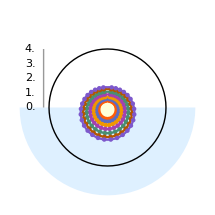
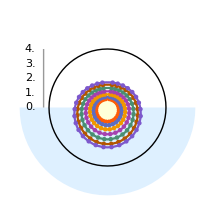
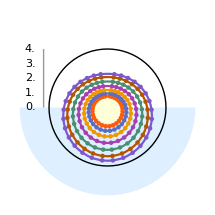
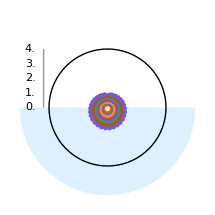

```mathematica
max = Max[#[[;;,;;,2]]]&/@data;
max = Max[max]
case = Table[i,{4},{i,.75,-.75,-.25}];
colorsPlot = {#,#,#,#}&@  colors[[2;;Length[data[[1]]]+1]]

plots = MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->max*1.65,
PolarAxesOrigin->{{Left,Up},max},
PlotStyle->Table[Directive[PointSize[.015],i],{i,#3}],
Evaluate[graphsOptsPolar],
PolarTicks->{None,Automatic},
Prolog->{LightBlue,Disk[{0,0}, max*1.65,{0,-Pi}],LightYellow,Disk[1*{0,0}/3.5,max /3.5]}
]&,
{data,case,colorsPlot}]
```

```mathematica
angle = ToString/@ {15,38,42,75}
MapIndexed[( name = angle[[First[#2]]];
  name = FileNameJoin[{"Internal-sp","5-Far-S","5-Far-SY-"<>name<>".pdf"}];
  Export[name,#1]
  )&, plots]
```

{15,38,42,75}

{Internal-sp/5-Far-S/5-Far-SY-15.pdf,Internal-sp/5-Far-S/5-Far-SY-38.pdf,Internal-sp/5-Far-S/5-Far-SY-42.pdf,Internal-sp/5-Far-S/5-Far-SY-75.pdf}

Far Field P (Normal X)

```mathematica
radius = 12.5;

cases = {7,6,5,1,2,3,4};
data = FileNames["3*csv","*p"];
data = data[[cases]];
data//TableForm

data =Drop[Import[#,"Data"],8]&/@ data;
data = Transpose@Map[Partition[#,51]&,data]; (*Separete eat wlength value*)

data//Dimensions
```

Internal-p/3-Abs-FarX-p75.csv
Internal-p/3-Abs-FarX-p50.csv
Internal-p/3-Abs-FarX-p25.csv
Internal-p/3-Abs-FarX-00.csv
Internal-p/3-Abs-FarX-m25.csv
Internal-p/3-Abs-FarX-m50.csv
Internal-p/3-Abs-FarX-m75.csv

{4,7,51,2}

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];
```

2.26314

{{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8]},{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8]},{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8]},{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8]}}

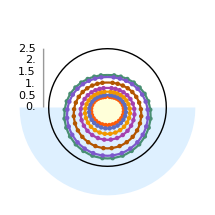
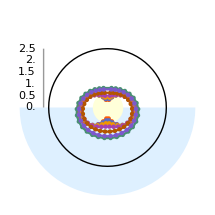
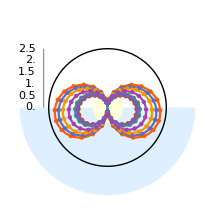
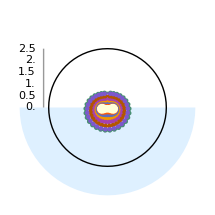

```mathematica
max = Max[#[[;;,;;,2]]]&/@data;
max = Max[max]
case = Table[i,{4},{i,.75,-.75,-.25}];
colorsPlot = {#,#,#,#}&@  colors[[2;;Length[data[[1]]]+1]]

plots = MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->max*1.65,
PolarAxesOrigin->{{Left,Up},max},
PlotStyle->Table[Directive[PointSize[.015],i],{i,#3}],
Evaluate[graphsOptsPolar],
PolarTicks->{None,Automatic},
Prolog->{LightBlue,Disk[{0,0}, max*1.65,{0,-Pi}],LightYellow,Disk[1*{0,0}/3.5,max /3.5]}
]&,
{data,case,colorsPlot}]
```

```mathematica
angle = ToString/@ {15,38,42,75}
MapIndexed[( name = angle[[First[#2]]];
  name = FileNameJoin[{"Internal-sp","6-Far-P","6-Far-PX-"<>name<>".pdf"}];
  Export[name,#1]
  )&, plots]
```

{15,38,42,75}

{Internal-sp/6-Far-P/6-Far-PX-15.pdf,Internal-sp/6-Far-P/6-Far-PX-38.pdf,Internal-sp/6-Far-P/6-Far-PX-42.pdf,Internal-sp/6-Far-P/6-Far-PX-75.pdf}

Far Field P (Normal Y)

```mathematica
radius = 12.5;

cases = {7,6,5,1,2,3,4};
data = FileNames["4*csv","*p"];
data = data[[cases]];
data//TableForm

data =Drop[Import[#,"Data"],8]&/@ data;
data = Transpose@Map[Partition[#,51]&,data]; (*Separete eat wlength value*)

data//Dimensions
```

Internal-p/4-Abs-FarY-p75.csv
Internal-p/4-Abs-FarY-p50.csv
Internal-p/4-Abs-FarY-p25.csv
Internal-p/4-Abs-FarY-00.csv
Internal-p/4-Abs-FarY-m25.csv
Internal-p/4-Abs-FarY-m50.csv
Internal-p/4-Abs-FarY-m75.csv

{4,7,51,2}

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];
```

2.30319

{{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8]},{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8]},{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8]},{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8]}}

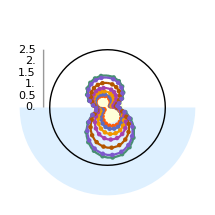
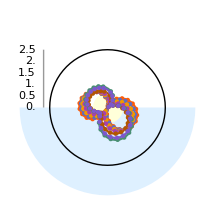
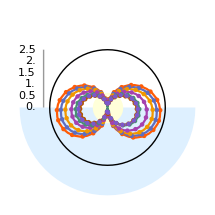
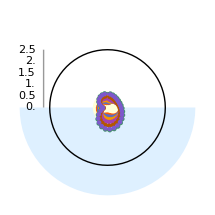

```mathematica
max = Max[#[[;;,;;,2]]]&/@data;
max = Max[max]
case = Table[i,{4},{i,.75,-.75,-.25}];
colorsPlot = {#,#,#,#}&@  colors[[2;;Length[data[[1]]]+1]]

plots = MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->max*1.65,
PolarAxesOrigin->{{Left,Up},max},
PlotStyle->Table[Directive[PointSize[.015],i],{i,#3}],
Evaluate[graphsOptsPolar],
PolarTicks->{None,Automatic},
Prolog->{LightBlue,Disk[{0,0}, max*1.65,{0,-Pi}],LightYellow,Disk[1*{0,0}/3.5,max /3.5]}
]&,
{data,case,colorsPlot}]
```

```mathematica
angle = ToString/@ {15,38,42,75}
MapIndexed[( name = angle[[First[#2]]];
  name = FileNameJoin[{"Internal-sp","6-Far-P","6-Far-PY-"<>name<>".pdf"}];
  Export[name,#1]
  )&, plots]
```

{15,38,42,75}

{Internal-sp/6-Far-P/6-Far-PY-15.pdf,Internal-sp/6-Far-P/6-Far-PY-38.pdf,Internal-sp/6-Far-P/6-Far-PY-42.pdf,Internal-sp/6-Far-P/6-Far-PY-75.pdf}